```mathematica
f2[x_]:=A2/(1+(x/B2)^h2)+basal2;
df2[x_]:=-(A2 h2 (x/B2)^(-1+h2))/(B2 (1+(x/B2)^h2)^2);

df2v2[x_]:=-h2/(A2*x)*(f2[x]-basal2)*(basal2+A2-f2[x])
```

```mathematica
h2v2[x_]:=h2/(A2*f2[x])*(f2[x]-basal2)*(basal2+A2-f2[x])
```

```mathematica
A2=57.6;
h2:=3.7;
B2:=160;
basal2:=0.52;
```

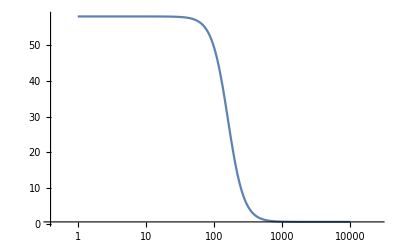

```mathematica
LogLinearPlot[f2[x],{x,1,10000}]
```

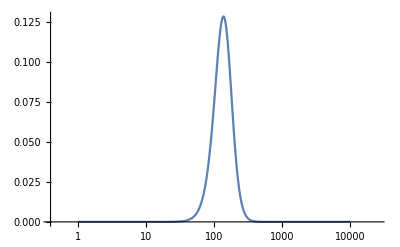

```mathematica
LogLinearPlot[(df2[x])^2,{x,1,10000},PlotRange->All]
```

```mathematica
LogLinearPlot[(df2v2[x])^2,{x,1,10000},PlotRange->All]
```

-Graphics-

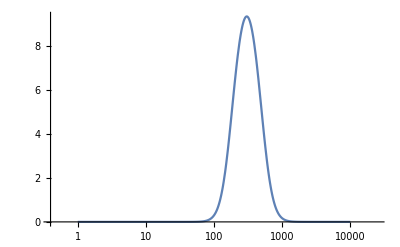

```mathematica
LogLinearPlot[(h2v2[x])^2,{x,1,10000},PlotRange->All]
```